```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<IsingScalingFunction`
```

## Checking Convergence

```mathematica
expansionData=
{Rest@(DScriptFPlusMinusDξθ0List@@PrepareArgument[Data[2]])[10],
Rest@(DScriptFPlusMinusDξθ0List@@PrepareArgument[Data[6]])[10],
DScriptMCasDξList[10,θ0Cas]Table[((m-1)!)/(m!),{m,1,11}]};
```

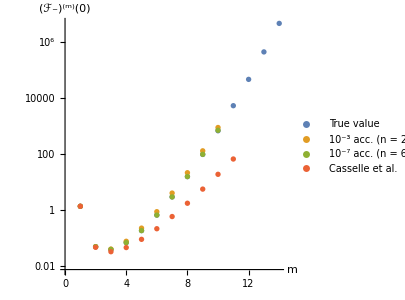

```mathematica
lowExpansion=ListLogPlot[Abs@Prepend[N@expansionData,Rest@Gls],
PlotLegends->{"True value","10^-3 acc. (n = 2)", "10^-7 acc. (n = 6)", "Casselle et al."},
AxesLabel->{m,"(ℱ_-)^(m)(0)"},AspectRatio->1,ImageSize->300,LabelStyle->{Black,FontSize->14,FontFamily->Times}
]
```

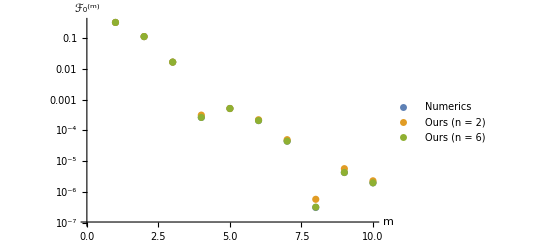

```mathematica
ListLogPlot[Abs@{
Rest@Φs,
Rest@(DScriptF0DηList@@PrepareArgument[Data[2]])[10,1],
Rest@(DScriptF0DηList@@PrepareArgument[Data[6]])[10,1]
},
PlotLegends->{"Numerics","Ours (n = 2)", "Ours (n = 6)"},
AxesLabel->{m,"ℱ_0^(m)"}
]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(371382927287350339456845128427992 2^(1/12) 11429856398034503^(1/8) ⅇ^(-1/8-«1») Glaisher^(3/2) (-1+ⅇ^((«1»)/(«1»)) ExpIntegralEi[-(«1»)/(«1»)]-(114355882310899360521914666542829 «3» ExpIntegralEi[-(114355882310899360521914666542829 («17»)^(«1») «1» π)/(107668955486287134775550584515499446643328 «3»)])/(107668955486287134775550584515499446643328 2^(1/12) 189336221^(3/4) Glaisher^(3/2))))/(1075985451139697449885706090335689 189336221^(1/4) π^2)-(371382927287350339456845128427992 «4» (1-ⅇ^((«1»)/(«1»)) ExpIntegralEi[«1»]+(114355882310899360521914666542829 «4»)/(107668955486287134775550584515499446643328 2^(«1») «1» («8»)^(3/2))))/(1075985451139697449885706090335689 189336221^(1/4) π^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(46681463692889041973700532620906696296885587180818594561 (-(371382927287350339456845128427992 2^(1«1»«2») «2» «1» (-1+ⅇ^Times[«7»] ExpIntegralEi[Times[«7»]]-(114355882310899360521914666542829 «3» «13»[«1»])/(«1»)))/(1075985451139697449885706090335689 189336221^(1/4) π^2)-(«1»)/(1075985451139697449885706090335689 («9»)^(«1») π^2)))/383435814415399100830298627422256492275580379991986176+(1995291215029551557786949 (-(371382927287350339456845128427992 2^(1/12) («17»)^(«1») «1» Glaisher^(3/2) («1»))/(1075985451139697449885706090335689 189336221^(1/4) π^2)-(«1»)/(«1»)+12 (-(«1»)/(«1»)-(«1»)/(«1»))))/104122350499534957937152.

General::stop: Further output of N::meprec will be suppressed during this calculation.

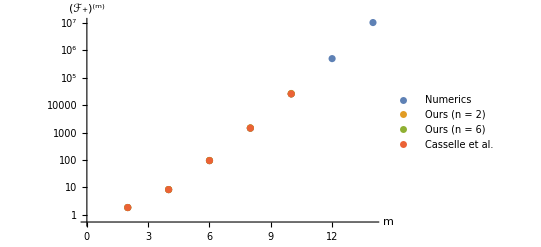

```mathematica
ListLogPlot[Abs@{
Rest@Ghs,
Rest@(DScriptFPlusMinusDξList@@PrepareArgument[Data[2]])[10,0],
Rest@(DScriptFPlusMinusDξList@@PrepareArgument[Data[6]])[10,0],
DScriptMCasDξList[9,0]Table[((m-1)!)/(m!),{m,1,10}]
},
PlotLegends->{"Numerics","Ours (n = 2)", "Ours (n = 6)", "Casselle et al."},
AxesLabel->{m,"(ℱ_+)^(m)"}
]
```

```mathematica
freeEnergyData=Table[{ut[1,γ Data[n]["θ0"]](uh[Data[n]["θ0"],Data[n]["gs"]][1,γ Data[n]["θ0"]])^(-8/15),Re@(DScriptF0DηList@@PrepareArgument[Data[n]])[0,γ Data[n]["θ0"]][[1]]},{n,2,6},Evaluate@N[{γ,10^-4,1-10^-4,10^-4},40]];
```

```mathematica
freeEnergyDataInterpolation=Interpolation/@freeEnergyData;
```

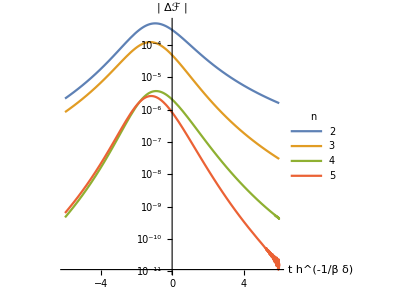

```mathematica
pCovergence=LogPlot[Evaluate[(Abs[#[x]-Last[freeEnergyDataInterpolation][x]])&/@Most[freeEnergyDataInterpolation]],{x,-6,6},PlotLegends->LineLegend[{2,3,4,5},LegendLabel->"n"],AxesLabel->{"t h^(-1/β δ)","| Δℱ |"},LabelStyle->{Black,FontSize->14,FontFamily->Times},ImageSize->300,AspectRatio->1]
```

```mathematica
magnetizationData=Table[{ut[1,γ Data[n]["θ0"]](uh[Data[n]["θ0"],Data[n]["gs"]][1,γ Data[n]["θ0"]])^(-8/15),Re@(DScriptF0DηList@@PrepareArgument[Data[n]])[1,γ Data[n]["θ0"]][[-1]]},{n,2,6},Evaluate@N[{γ,10^-4,1-10^-4,10^-4},30]];
```

```mathematica
magnetizationDataInterpolation=Interpolation/@magnetizationData;
```

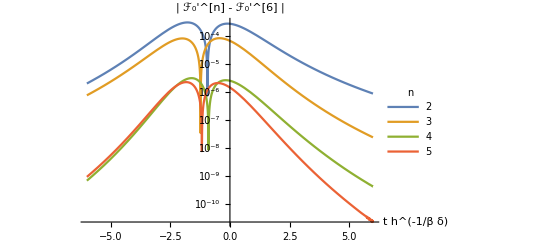

```mathematica
LogPlot[Evaluate[(Abs[#[x]-Last[magnetizationDataInterpolation][x]])&/@Most[magnetizationDataInterpolation]],{x,-6,6},PlotLegends->LineLegend[{2,3,4,5},LegendLabel->"n"],AxesLabel->{"t h^(-1/β δ)","| ℱ_0'^[n] - ℱ_0'^[6] |"},LabelStyle->{Black,FontSize->12}]
```

## Plotting as functions of scaling invariants

```mathematica
η2=η[Data[2]["θ0"],Data[2]["gs"]];
ξ2=ξ[Data[2]["θ0"],Data[2]["gs"]];
DScriptF0Dη2=DScriptF0Dη@@PrepareArgument[Data[2]];
DufDuh2=DufDuh@@PrepareArgument[Data[2]];
η6=η[Data[6]["θ0"],Data[6]["gs"]];
ξ6=ξ[Data[6]["θ0"],Data[6]["gs"]];
DScriptF0Dη6=DScriptF0Dη@@PrepareArgument[Data[6]];
DufDuh6=DufDuh@@PrepareArgument[Data[6]];
```

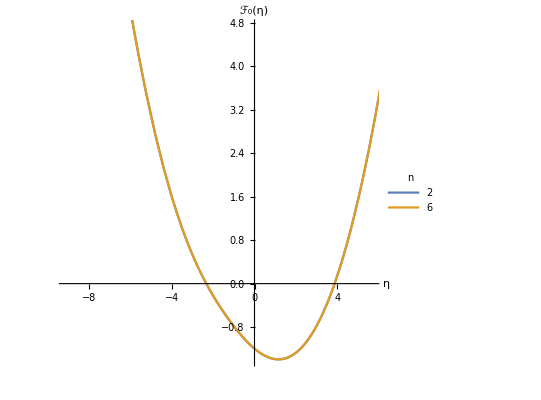

```mathematica
ParametricPlot[Evaluate@{
{η2[γ Data[2]["θ0"]],DScriptF0Dη2[0,γ Data[2]["θ0"]]},
{η6[γ Data[6]["θ0"]],DScriptF0Dη6[0,γ Data[6]["θ0"]]}
},{γ,0,0.999},
AspectRatio->1,AxesLabel->{η,Subscript[ℱ, 0][η]},LabelStyle->Black,PlotLegends->LineLegend[{2,6},LegendLabel->"n"]
]
```

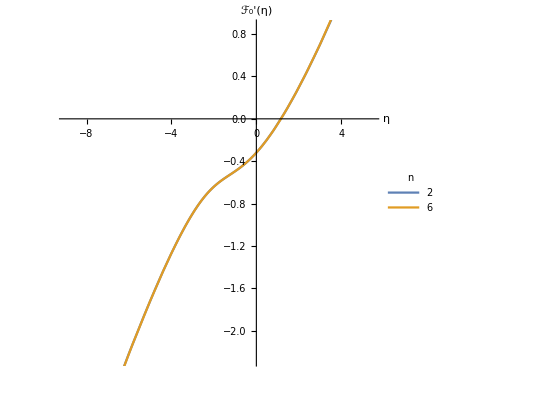

```mathematica
ParametricPlot[Evaluate@{
{η2[γ Data[2]["θ0"]],DScriptF0Dη2[1,γ Data[2]["θ0"]]},
{η6[γ Data[6]["θ0"]],DScriptF0Dη6[1,γ Data[6]["θ0"]]}
},{γ,0,0.999},
AspectRatio->1,AxesLabel->{η,Subscript[ℱ, 0]'[η]},LabelStyle->Black,PlotLegends->LineLegend[{2,6},LegendLabel->"n"]
]
```

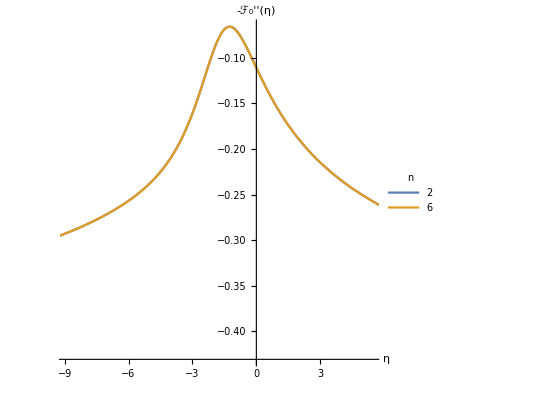

```mathematica
ParametricPlot[Evaluate@{
{η2[γ Data[2]["θ0"]],-DScriptF0Dη2[2,γ Data[2]["θ0"]]},
{η6[γ Data[6]["θ0"]],-DScriptF0Dη6[2,γ Data[6]["θ0"]]}
}
,{γ,0,0.999},
AspectRatio->1,AxesLabel->{η,-Subscript[ℱ, 0]''[η]},LabelStyle->Black,PlotLegends->LineLegend[{2,6},LegendLabel->"n"]
]
```

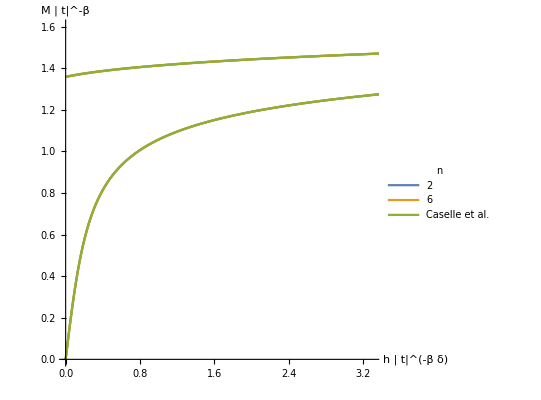

```mathematica
ParametricPlot[Evaluate@{
{ξ2[γ Data[2]["θ0"]],-DufDuh2[1][3,γ Data[2]["θ0"]] Abs[ut[3,γ Data[2]["θ0"]]]^(-1/8)},
{ξ6[γ Data[6]["θ0"]],-DufDuh6[1][3,γ Data[6]["θ0"]] Abs[ut[3,γ Data[6]["θ0"]]]^(-1/8)},
{ξ[θ0Cas,gsCas][γ θ0Cas],DScriptMCasDξList[0,γ θ0Cas][[-1]]}
},{γ,0,0.999},PlotRange->{{0,3.3},{0,1.6}},
AspectRatio->1,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","M | t|^-β"},LabelStyle->{Black,FontSize->14},PlotLegends->LineLegend[{2,6,"Caselle et al."},LegendLabel->"n"]
]
```

ParametricPlot::precw: The precision of the argument function ({((1-1. γ^2) (0.295091 γ-0.0767491 γ^3-0.0175761 γ^5-0.00699026 γ^7-0.00395703 γ^9))/(RealAbs[-1+1.16951 γ^2]^(15/8)),0.+(-(0.294427 γ^2 (-1+1.16951 Power[«2»]))/RealAbs[Plus[«2»]]^(17/8)+1.00701/RealAbs[Plus[«2»]]^(1/8))/(-(4.0554 γ (1+Times[«2»]) (-1+Times[«2»]) (Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]))/RealAbs[«1»]^(31/8)+((1+Times[«2»]) («1»))/RealAbs[«1»]^(15/8)-(1.84939 γ (Times[«2»]+«3»+Times[«2»]))/RealAbs[«1»]^(15/8))}) is less than WorkingPrecision (20.).

ParametricPlot::precw: The precision of the argument function ({(-(4.0554 γ (1-1. γ^2) (-1+1.16951 γ^2) (0.295091 γ-0.0767491 γ^3-0.0175761 γ^5-0.00699026 γ^7-0.00395703 γ^9))/RealAbs[-1+Times[«2»]]^(31/8)+((1-1. γ^2) (0.272869-0.212908 γ^2-0.0812625 γ^4-0.045247 γ^6-0.0329314 γ^8))/RealAbs[-1+Times[«2»]]^(15/8)-(1.84939 γ (0.295091 γ-0.0767491 γ^3-0.0175761 γ^5-0.00699026 γ^7-0.00395703 γ^9))/RealAbs[-1+Times[«2»]]^(15/8))-0,(-1+1.16951 γ^2)-0,(1-1.16951 γ^2)-0}) is less than WorkingPrecision (20.).

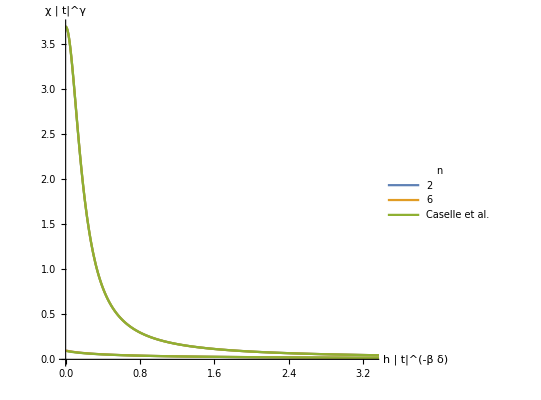

```mathematica
ParametricPlot[Evaluate@{
{ξ2[γ Data[2]["θ0"]],-DufDuh2[2][1,γ Data[2]["θ0"]] Abs[ut[1,γ Data[2]["θ0"]]]^(7/4)},
{ξ6[γ Data[6]["θ0"]],-DufDuh6[2][1,γ Data[6]["θ0"]] Abs[ut[1,γ Data[6]["θ0"]]]^(7/4)},
{ξ[θ0Cas,gsCas][γ θ0Cas],DScriptMCasDξList[1,γ θ0Cas][[-1]]}
},{γ,0,0.999},PlotRange->{{0,3.3},Automatic},
AspectRatio->1,WorkingPrecision->20,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","χ | t|^γ"},LabelStyle->{Black,FontSize->14},PlotLegends->LineLegend[{2,6,"Caselle et al."},LegendLabel->"n"]
]
```

## Applications: plotting as functions of control variables (t and h)

```mathematica
invCoords6=InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]];
DufDut6=DufDut@@PrepareArgument[Data[6]];
```

### Entropy

In this plot, we show (∂u_f)/(∂u_t), which is the singular part of the entropy (modulo a constant analytic factor) near the transition.

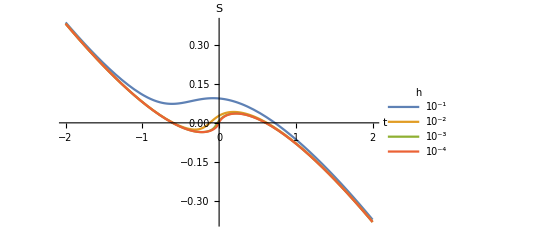

```mathematica
Plot[{
-Re[DufDut6[1]@@invCoords6[t,10^-1]],
-Re[DufDut6[1]@@invCoords6[t,10^-2]],
-Re[DufDut6[1]@@invCoords6[t,10^-3]],
-Re[DufDut6[1]@@invCoords6[t,10^-4]]
},{t,-2,2},PlotRange->All,Exclusions->None,AxesLabel->{t,"S"},LabelStyle->Black,PlotLegends->LineLegend[{"10^-1","10^-2","10^-3","10^-4"},LegendLabel->h]]
```

### Specific heat

In this plot, we show (∂^2 u_f)/(∂u_t^2), which is the singular part of the specific heat (modulo a constant analytic factor) near the transition.

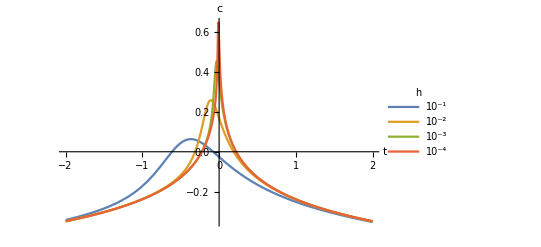

```mathematica
Plot[{
-Re[DufDut6[2]@@invCoords6[t,10^-1]],
-Re[DufDut6[2]@@invCoords6[t,10^-2]],
-Re[DufDut6[2]@@invCoords6[t,10^-3]],
-Re[DufDut6[2]@@invCoords6[t,10^-4]]
},{t,-2,2},PlotRange->All,Exclusions->None,AxesLabel->{t,"c"},LabelStyle->Black,PlotLegends->LineLegend[{"10^-1","10^-2","10^-3","10^-4"},LegendLabel->h]]
```

### Magnetization

In this plot, we show (∂u_f)/(∂u_h), which is the singular part of the magnetization (modulo a constant analytic factor) near the transition. Notice here, as in all plots using this library, that t∝T_c-T (the negative of the usual sense) following conventions in high energy physics.

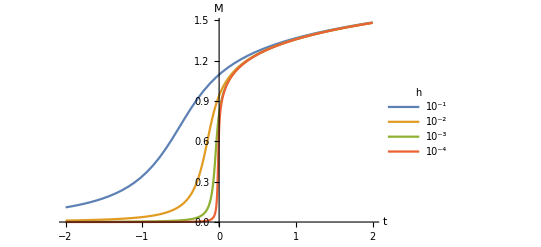

```mathematica
Plot[{
-Re[DufDuh6[1]@@invCoords6[t,10^-1]],
-Re[DufDuh6[1]@@invCoords6[t,10^-2]],
-Re[DufDuh6[1]@@invCoords6[t,10^-3]],
-Re[DufDuh6[1]@@invCoords6[t,10^-4]]
},{t,-2,2},PlotRange->All,Exclusions->None,AxesLabel->{t,"M"},LabelStyle->Black,PlotLegends->LineLegend[{"10^-1","10^-2","10^-3","10^-4"},LegendLabel->h]]
```

### Susceptibility

In this plot, we show (∂^2 u_f)/(∂u_h^2), which is the singular part of the susceptibility (modulo a constant analytic factor) near the transition.

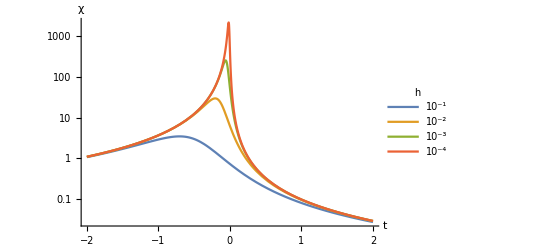

```mathematica
LogPlot[{
-Re[DufDuh6[2]@@invCoords6[t,10^-1]],
-Re[DufDuh6[2]@@invCoords6[t,10^-2]],
-Re[DufDuh6[2]@@invCoords6[t,10^-3]],
-Re[DufDuh6[2]@@invCoords6[t,10^-4]]
},{t,-2,2},Exclusions->None,PlotRange->All,AxesLabel->{t,"χ"},LabelStyle->Black,PlotLegends->LineLegend[{"10^-1","10^-2","10^-3","10^-4"},LegendLabel->h]]
```